# Theory

## Symmetry of the spectrum of linear combinations of Pauli strings

```mathematica
II := IdentityMatrix[2]
X:=PauliMatrix[1]
Y:=PauliMatrix[2]
Z := PauliMatrix[3]
```

```mathematica
A[c0_,c1_,c2_,c3_]:=c0*II+c1*X+c2*Y+c3*Z
Commutator[A_,B_]:=A.B-B.A
Anticommutator[A_,B_]:=Simplify[A.B+B.A]
```

## Building a counter - example

### With different Pauli weights

(0 | 0 | 0 | 0
0 | 5 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | -3)

(5 | -3 | 0 | 0
{0,1,0,0} | {0,0,0,1} | {0,0,1,0} | {1,0,0,0})

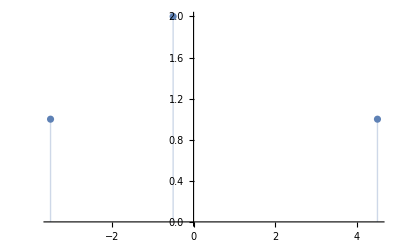

```mathematica
H:=5*(1/4)*KroneckerProduct[II+Z,II-Z]-3*(1/4)*KroneckerProduct[II-Z,II-Z]
P:=-(1/2)*KroneckerProduct[II,Z]+2*KroneckerProduct[Z,II]-2*KroneckerProduct[Z,Z]
H//MatrixForm
TraditionalForm[Simplify[Eigensystem[H]]]
{e,v}=Eigensystem[P];
ListPlot[Counts[Round[e,0.01]],Filling->Axis]
```

### With same Pauli weights

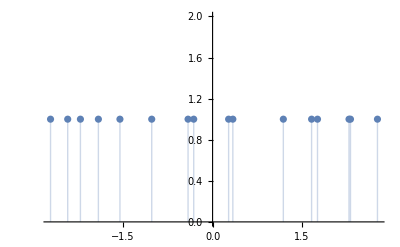

{-2.72039,-2.43222,-2.21871,-1.91707,-1.55528,-1.02167,-0.411766,-0.316708,0.269232,0.340028,1.18779,1.66221,1.76129,2.29037,2.31494,2.76795}

```mathematica
P:=+0.3408*KroneckerProduct[Z,Y,Y,X]+ 0.8292*KroneckerProduct[X,Y,X,Y]+ 0.8588*KroneckerProduct[X,Z,X,Y]+ 0.1153*KroneckerProduct[X,X,Z,X]+ 0.4606*KroneckerProduct[Z,Y,X,Y]+ 0.2942*KroneckerProduct[Y,X,Y,Z]+ 0.8334*KroneckerProduct[Y,Z,Z,X]+ 0.8144*KroneckerProduct[Y,Y,Y,Z]
{e,v}=Eigensystem[P];
ListPlot[Counts[e],Filling->Axis]
Sort[e]
```

### Finding the cause of the asymmetry

Putting all coefficients to 1 -> still asymmetric
Reducing to a single term -> symmetric

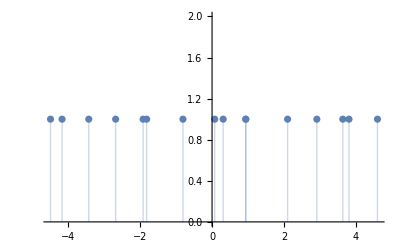

{Root-4.17Root[80-192 #1-320 #1^2+256 #1^3+264 #1^4-16 #1^5-32 #1^6+#1^8&,1]-4.173814556339476,Root-2.68Root[80-192 #1-320 #1^2+256 #1^3+264 #1^4-16 #1^5-32 #1^6+#1^8&,2]-2.6834447778982984,Root-1.82Root[80-192 #1-320 #1^2+256 #1^3+264 #1^4-16 #1^5-32 #1^6+#1^8&,3]-1.8208098667080428,Root-0.810Root[80-192 #1-320 #1^2+256 #1^3+264 #1^4-16 #1^5-32 #1^6+#1^8&,4]-0.8096292291454045,Root0.309Root[80-192 #1-320 #1^2+256 #1^3+264 #1^4-16 #1^5-32 #1^6+#1^8&,5]0.30901728455829763,Root0.936Root[80-192 #1-320 #1^2+256 #1^3+264 #1^4-16 #1^5-32 #1^6+#1^8&,6]0.9358702389723746,Root3.64Root[80-192 #1-320 #1^2+256 #1^3+264 #1^4-16 #1^5-32 #1^6+#1^8&,7]3.639618411702598,Root4.60Root[80-192 #1-320 #1^2+256 #1^3+264 #1^4-16 #1^5-32 #1^6+#1^8&,8]4.603192494857952,Root-4.49Root[-48+704 #1-704 #1^2-256 #1^3+296 #1^4+16 #1^5-32 #1^6+#1^8&,1]-4.494962361440714,Root-3.43Root[-48+704 #1-704 #1^2-256 #1^3+296 #1^4+16 #1^5-32 #1^6+#1^8&,2]-3.4313263824617617,Root-1.92Root[-48+704 #1-704 #1^2-256 #1^3+296 #1^4+16 #1^5-32 #1^6+#1^8&,3]-1.9185228951866569,Root0.0738Root[-48+704 #1-704 #1^2-256 #1^3+296 #1^4+16 #1^5-32 #1^6+#1^8&,4]0.07375503482824526,Root0.941Root[-48+704 #1-704 #1^2-256 #1^3+296 #1^4+16 #1^5-32 #1^6+#1^8&,5]0.9411698709440883,Root2.10Root[-48+704 #1-704 #1^2-256 #1^3+296 #1^4+16 #1^5-32 #1^6+#1^8&,6]2.1025991067976872,Root2.92Root[-48+704 #1-704 #1^2-256 #1^3+296 #1^4+16 #1^5-32 #1^6+#1^8&,7]2.9163074817944166,Root3.81Root[-48+704 #1-704 #1^2-256 #1^3+296 #1^4+16 #1^5-32 #1^6+#1^8&,8]3.810980144724695}

```mathematica
P:=KroneckerProduct[Z,Y,Y,X]+ KroneckerProduct[X,Y,X,Y]+KroneckerProduct[X,Z,X,Y]+ KroneckerProduct[X,X,Z,X]+KroneckerProduct[Z,Y,X,Y]+ KroneckerProduct[Y,X,Y,Z]+ KroneckerProduct[Y,Z,Z,X]+KroneckerProduct[Y,Y,Y,Z]
{e,v}=Eigensystem[P];
ListPlot[Counts[e],Filling->Axis]
Sort[e]
```

### Creating a new example

```mathematica
SymmetryCheckList[tuplelist_]:=(
listsymmetry=True;
For[t=1,t≤ Dimensions[tuplelist],t++,
SymmetryCheck[tuplelist⟦t⟧];
listsymmetry=listsymmetry&&symmetry];
If[listsymmetry,Print["All symmetric"],]
)
SymmetryCheck[tuple_]:=(
r=Dimensions[tuple]⟦1⟧;
H=∑_(j=1)^r tuple⟦j⟧;
A=Counts[Eigensystem[H]⟦1⟧];
Asort=KeySort[A];
evalcount=Dimensions[Keys[A]]⟦1⟧;
symmetry=True;
For[i=1,i≤ Floor[evalcount/2],i++,
test1=Keys[Asort]⟦i⟧==Keys[Asort]⟦-i⟧;
test2=Asort[Keys[Asort]⟦i⟧]==Asort[Keys[Asort]⟦-i⟧];
symmetry=symmetry&&test1&&test2];
If[symmetry,,Print[H]];
)
```

#### Checking the function

```mathematica
P={0.3408*KroneckerProduct[Z,Y,Y,X], 0.8292*KroneckerProduct[X,Y,X,Y], 0.8588*KroneckerProduct[X,Z,X,Y], 0.1153*KroneckerProduct[X,X,Z,X], 0.4606*KroneckerProduct[Z,Y,X,Y], 0.2942*KroneckerProduct[Y,X,Y,Z], 0.8334*KroneckerProduct[Y,Z,Z,X], 0.8144*KroneckerProduct[Y,Y,Y,Z]};
SymmetryCheck[P]
```

#### 2 qubit case -> brute force

```mathematica
list = KroneckerProduct@@@Tuples[{X,Y,Z},2];
terms = 6;
combinations = Tuples[list,terms];
combcount=Dimensions[combinations]⟦1⟧
SymmetryCheckList[combinations]
```

531441

All symmetric

#### 3 qubit case -> brute force

```mathematica
list = KroneckerProduct@@@Tuples[{X,Y,Z},3];
terms = 6;
combinations = Tuples[list,terms];
combcount=Dimensions[combinations]⟦1⟧
SymmetryCheckList[combinations]
```

387420489

All symmetric

#### 4 qubit case -> brute force

```mathematica
list = KroneckerProduct@@@Tuples[{X,Y,Z},4];
terms = 4;
combinations = Tuples[list,terms];
combcount=Dimensions[combinations]⟦1⟧
SymmetryCheckList[combinations]
```

43046721

All symmetric

#### 4 qubit case

Starting from single term, all X 	-> XXXX					-> symmetric (2 evals)
Adding 1 term, 1 changed Pauli 	-> XXXX + XXXZ 			-> symmetric (2 evals)
2 terms, all different Paulis 		-> XXXX + ZZZZ			-> symmetric but with 0 evals (3 evals)	
3 terms						-> XXXX + XXXZ + ZZZZ		-> symmetric (4 evals)

```mathematica
P:=KroneckerProduct[X,X,X,X]+ KroneckerProduct[X,X,X,Z]+ KroneckerProduct[Y,X,X,X]+ KroneckerProduct[X,Y,X,X]
{e,v}=Eigensystem[P];
Counts[e]
```

<|-√10→2,√10→2,-√2→6,√2→6|>

## X + Y + Z example

```mathematica
P:=X+Y+Z
B=Table[Subscript[b,i,j],{i,2},{j,2}];
B⟦2,1⟧=B⟦1,2⟧*;
{e,v}=Eigensystem[P];
Sort[e]
P//MatrixForm
B//MatrixForm
Anticommutator[P,B]//MatrixForm
Anticommutator[P,A[0,ar,-ai,-ar+ai]]//MatrixForm
```

{-√3,√3}

(1 | 1-ⅈ
1+ⅈ | -1)

(b_(1,1) | b_(1,2)
Conjugate[b_(1,2)] | b_(2,2))

((1-ⅈ) Conjugate[b_(1,2)]+2 b_(1,1)+(1+ⅈ) b_(1,2) | (1-ⅈ) (b_(1,1)+b_(2,2))
(1+ⅈ) (b_(1,1)+b_(2,2)) | (1-ⅈ) Conjugate[b_(1,2)]+(1+ⅈ) b_(1,2)-2 b_(2,2))

(0 | 0
0 | 0)

```mathematica
{e,v}=Eigensystem[P]
A[0,ar,-ai,-ar+ai].v⟦1⟧
A[0,ar,-ai,-ar+ai].v⟦2⟧
```

{{-√3,√3},{{(-1/2+ⅈ/2) (-1+√3),1},{(1/2-ⅈ/2) (1+√3),1}}}

{ⅈ ai-(1/2-ⅈ/2) (-1+√3) (ai-ar)+ar,-ai+ar-(1/2-ⅈ/2) (-1+√3) (-ⅈ ai+ar)}

{ⅈ ai+(1/2-ⅈ/2) (1+√3) (ai-ar)+ar,-ai+ar+(1/2-ⅈ/2) (1+√3) (-ⅈ ai+ar)}

## -XX - YY - ZZ example

```mathematica
P:=-KroneckerProduct[Z,Z,II]-KroneckerProduct[II,X,X]-KroneckerProduct[Y,II,Y]
{e,v}=Eigensystem[P];
Sort[e]
```

{-√3,-√3,-√3,-√3,√3,√3,√3,√3}